## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Глаголев Я.О. Группа: ТФ-13-22 Задача № 3

### -Graphics-

#### Введем исходные данные:

```mathematica
d0=UnitConvert[Quantity[400,"Millimeters"],"Meters"];

r0=d0/2;L=Quantity[0.6,"Meters"];t0=Quantity[650,"DegreesCelsius"];tLiquid=Quantity[20,"DegreesCelsius"];α=Quantity[80,("Watts")/(("Meters")^2*"Kelvins")];
ρ=Quantity[2787,("Kilograms")/("Meters")^3];
cp=Quantity[833,("Joules")/("Kilograms"*"Kelvins")];
λ=Quantity[164,("Watts")/("Meters"*"Kelvins")];
τ1=UnitConvert[Quantity[5,"Minutes"],"Seconds"];
```

#### Найдем коэффициент температуропроводности a:

```mathematica
a=UnitConvert[N[λ/(cp*ρ)],("Meters")^2/("Seconds")]
```

0.0000706418 m^2/s

#### Числа Био по радиальному( BiRadial) и вертикальному( BiVertical) направлениям:

```mathematica
BiRadial=N[(α*r0)/λ]
```

0.097561

```mathematica
BiVertical=N[(α*L/2)/λ]
```

0.146341

#### Числа Фурье по радиальному( FoRadial) и вертикальному( FoVertical) направлениям:

```mathematica
FoRadial=(a*τ1)/(r0)^2
```

0.529814

```mathematica
FoVertical=(a*τ1)/(L/2)^2
```

0.235473

#### Приступим к поиску корней характеристического уравнения(MATLAB) в радиальном направлении: -Graphics-

```mathematica
ϵ={0.4364   , 3.8571    ,7.0295   ,10.1831 ,  13.3310   ,16.4766 ,  19.6208};
```

#### В вертикальном направлении: -Graphics-

```mathematica
μ={0.3735    ,3.1875 ,   6.3064   , 9.4403,   12.5780,   15.7173   ,18.8573};
```

#### Найдем функцию распределения температуры в радиальном направлении:

```mathematica
ΘRadial[r_,τ_]:=Total[(2*BesselJ[1,ϵ])/(ϵ*(BesselJ[0,ϵ]+BesselJ[1,ϵ]^2))*BesselJ[0,ϵ*r/QuantityMagnitude[r0]]*Exp[-ϵ^2*QuantityMagnitude[a]*τ/QuantityMagnitude[r0]^2]];
```

```mathematica
ΘRadial[0,0]
```

0.999305

```mathematica
tRadial[r_,τ_]=tLiquid+(t0-tLiquid)*ΘRadial[r,τ];
```

#### Найдем температуру на оси цилиндра в момент времени τ = 0

```mathematica
tRadial[0,0]
```

922.712 K

```mathematica
UnitConvert[tRadial[0,0],"DegreesCelsius"]
```

649.562 °C

#### Найдем функцию распределения температуры в вертикальном направлении:

```mathematica
ΘVertical[x_,τ_]:=Total[(2*Sin[μ])/(μ+Sin[μ]*Cos[μ])*Cos[μ*x/QuantityMagnitude[L/2]]*Exp[-μ^2*(QuantityMagnitude[a]*τ)/QuantityMagnitude[(L/2)^2]]]
```

```mathematica
ΘVertical[0,0]
```

1.00033

```mathematica
tVertical[x_,τ_]:=tLiquid + (t0-tLiquid)*ΘVertical[x,τ];
```

#### Найдем температуру в центре цилиндра в момент времени τ = 0

```mathematica
tVertical[0,0]
```

923.356 K

```mathematica
UnitConvert[tVertical[0,0],"DegreesCelsius"]
```

650.206 °C

#### Найдем функцию распределения температурного поля в цилиндре t(x,r,τ)

```mathematica
Θ3D[x_,r_,τ_]:=ΘVertical[x,τ]*ΘRadial[r,τ];
```

```mathematica
t[x_,r_,τ_]:=tLiquid + (t0-tLiquid)*Θ3D[x,r,τ];
```

#### Начнем расчет температурного поля Сначала для r=0:

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.3 m | 534.926 °C
0.225 m | 551.064 °C
0.15 m | 561.949 °C
0.075 m | 568.092 °C
0. | 570.06 °C)

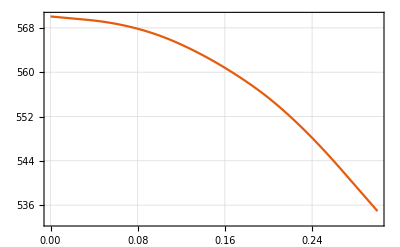

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для r=r0

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.3 m | 510.696 °C
0.225 m | 526.075 °C
0.15 m | 536.447 °C
0.075 m | 542.302 °C
0. | 544.177 °C)

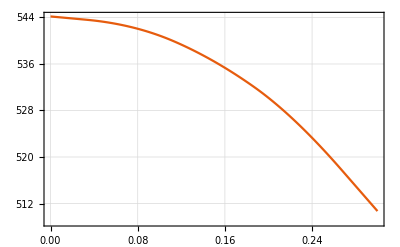

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=0

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.2 m | 544.177 °C
0.15 m | 555.423 °C
0.1 m | 563.53 °C
0.05 m | 568.424 °C
0. | 570.06 °C)

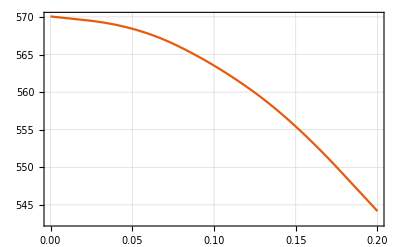

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=L/2

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.2 m | 510.696 °C
0.15 m | 521.224 °C
0.1 m | 528.813 °C
0.05 m | 533.394 °C
0. | 534.926 °C)

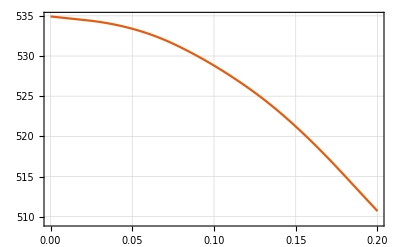

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Покажем распределение температуры в центре цилиндра и на расстоянии 0.2 d_0 от поверхности как функцию времени Сначала для центра:

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[3]}]//MatrixForm
```

(300. s | 570.06 °C
600. s | 502.339 °C
900. s | 442.05 °C)

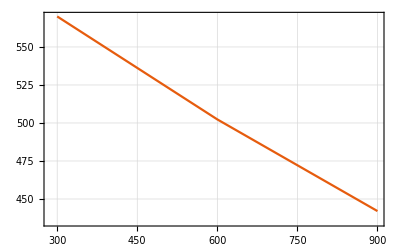

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[3]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь на расстоянии 0.2 d_0 (0.4 r_0)от поверхности , следовательно r=0.6 r_0)

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[3]}]//MatrixForm
```

(300. s | 560.669 °C
600. s | 494.108 °C
900. s | 434.847 °C)

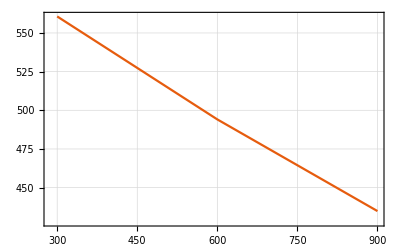

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[3]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Для определения темпа охлаждения и коэффициента температуропроводности заготовки построит несколько зависимостей ln(θ) используя данные полученные выше( в центре и на 0.6r_0). θ = t-tLiquid

```mathematica
lnForCenter=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[3]}]
```

{{300. s,6.31003},{600. s,6.17865},{900. s,6.04512}}

```mathematica
lnForPoint6r0=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[3]}]
```

{{300. s,6.29281},{600. s,6.16143},{900. s,6.02791}}

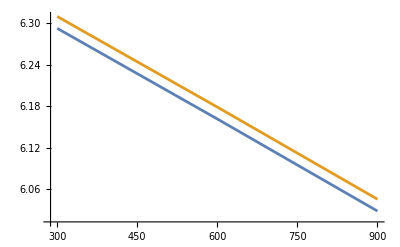

```mathematica
ListLinePlot[{lnForPoint6r0,lnForCenter}]
```

#### Нетрудно заметить,что стадии. регулярного режима гарантированно соответствует интервал [400,900] s. Найдем число Фурье в краевых точках интервала регулярного режима и удостоверимся что оно больше 0.3

```mathematica
FoRadialAt400=(a*Quantity[400,"Seconds"])/r0^2
```

0.706418

```mathematica
FoRadialAt900=(a*Quantity[900,"Seconds"])/r0^2
```

1.58944

```mathematica
FoVerticalAt400=(a*Quantity[400,"Seconds"])/(L/2)^2
```

0.313964

```mathematica
FoVerticalAt900=(a*Quantity[900,"Seconds"])/(L/2)^2
```

0.706418

#### Приступим к поиску темпа охлаждения m для наших двух точек

```mathematica
mAtCenter=Log[Θ3D[0,0,400]/Θ3D[0,0,900]]/Quantity[900-400,"Seconds"]
```

0.00044349 per second

```mathematica
mAtPoint6r0=Log[Θ3D[0,QuantityMagnitude[0.6*r0],400]/Θ3D[0,QuantityMagnitude[0.6*r0],900]]/Quantity[900-400,"Seconds"]
```

0.00044349 per second

#### Берем среднее

```mathematica
m=(mAtCenter+mAtPoint6r0)/2
```

0.00044349 per second

#### Fo > 0.3 поэтому ряд Фурье сходится быстро и первый член достаточно описывает все решение. Найдем коэффициент формы K:

```mathematica
K=1/((First[ϵ]/r0)^2+(First[μ]/(L/2))^2)
```

0.15845 m^2

#### Найдем коэффициент температуропроводности по второй теореме Кондратьева(допущение что наше m=m_∞) и сравним с теоретическим:

```mathematica
aExperimental=K*m
```

0.0000702709 m^2/s

```mathematica
a
```

0.0000706418 m^2/s

```mathematica
δa=Abs[a-aExperimental]/a
```

0.00525112

#### Найдем количество теплоты, отданное цилиндром за время τ_1: Для начала найдем сколько теплоты он отдаст до того момента как Θ==1 т.е. t=tLiquid

```mathematica
Q=N[π*(r0)^2*L*ρ*cp*(t0-tLiquid)]
```

1.10277×10^8 J

```mathematica
ΘRadialAverage=Total[(4*BiRadial^2)/(ϵ^2*(ϵ^2+BiRadial^2))*Exp[-ϵ^2*FoRadial]]
```

0.9038

```mathematica
ΘVerticalAverage=Total[(2*Sin[μ]^2)/(μ^2+μ*Sin[μ]*Cos[μ])*Exp[-μ^2*FoVertical]]
```

0.967292

```mathematica
ΘAverage=ΘVerticalAverage*ΘRadialAverage
```

0.874239

```mathematica
Qτ1=Q(1-ΘAverage)
```

1.38685×10^7 J

#### Подытожим полным температурным полем в момент времени τ_1

```mathematica
Show[ListLinePlot3D[Table[t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]],{x,0,L/2,L/4},{r,0,r0,r0/4}]],Boxed->False]
```

-Graphics3D-

```mathematica
data=Flatten[Table[{x,r,t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]]},{x,0,L/2,L/4},{r,0,r0,r0/4}],1];

ListPlot3D[data,Boxed->True,Mesh->None,PlotStyle->Directive[Opacity[0.7],Yellow],AxesLabel->{"x (m)","r (m)","t (°C)"},LabelStyle->Directive[Medium,Black],InterpolationOrder->4]
```

-Graphics3D-